```mathematica
DSolve[f'[x]==ⅇ^(x^2+y^2),f,x]
```

{{f→Function[{x},C[1]+1/2 ⅇ^(y^2) √π Erfi[x]]}}

```mathematica
Series[Erfi[x],{x,0,40}]*(1/2  √π)
```

x+x^3/3+x^5/10+x^7/42+x^9/216+x^11/1320+x^13/9360+x^15/75600+x^17/685440+x^19/6894720+x^21/76204800+x^23/918086400+x^25/11975040000+x^27/168129561600+x^29/2528170444800+x^31/40537905408000+x^33/690452066304000+x^35/12449059983360000+x^37/236887827111936000+x^39/4744158915944448000+O[x]^41

```mathematica
g[a_,y_]:=1/2 ⅇ^(y^2) √π Erfi[a]-Normal[Series[Erfi[x],{x,0,40}]*(1/2 ⅇ^(y^2) √π)]/.x->a
```

```mathematica
g[2, 2Sqrt[2]]//N
```

0.0000801363

```mathematica
Plot3D[g[a,b],{a,-2,2},{b,-5,5}]
```

-Graphics3D-

```mathematica
(*Computes weighted surface area for 2D bubble-in-bubble configuration*)
surf2d[V1_,V2_]:=N[2(V1+Pi)( Log[1+(V1/Pi)])^(1/2)+2(V1+V2+Pi)( Log[1+((V1+V2)/Pi)])^(1/2)]
```

```mathematica
surf2d[.005,20]
```

65.6722

```mathematica
(*Computes weighted surface area for 3D bubble-in-bubble configuration*)
surf3d[V1_,V2_]:=Module[{r1, r2,surf},
r1=r/.FindRoot[Integrate[4Pi r^2 ⅇ^(r^2),r]==V1,{r,0.01}];
r2=r/.FindRoot[Integrate[4Pi r^2 ⅇ^(r^2),r]==V2+V1,{r,0.01}];
surf=4Pi(r1^2ⅇ^(r1^2)+r2^2ⅇ^(r2^2));
Return[{surf,r1, r2}]]
```

```mathematica
surf3d[.005,20]
```

{83.1751,0.105841,1.22052}

```mathematica
r1=1;
r2=3;
```

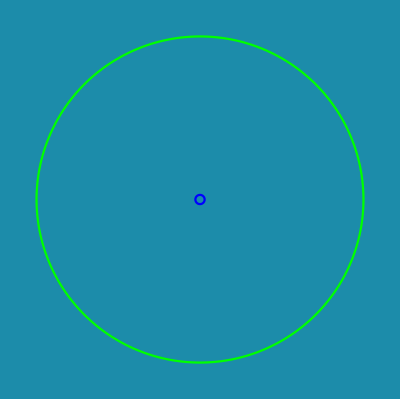

```mathematica
Module[{V1=0.005,V2=20,r1,r2},
r1=( Log[1+(V1/Pi)])^(1/2);
r2=( Log[1+((V1+V2)/Pi)])^(1/2);
ParametricPlot[{{r1 Cos[t],r1 Sin[t]},{r2 Cos[t],r2 Sin[t]}},{t, 0,2Pi},Axes->False,PlotStyle->{Blue,Green},Background->RGBColor[0.110, 0.549, 0.667]]]
```

```mathematica
Module[{V1=0.005,V2=20,r1, r2},
r1=surf3d[V1,V2][[2]];
r2=surf3d[V1,V2][[3]];
SphericalPlot3D[{r1, r2},{θ,0,Pi},{ϕ,0,2Pi},PlotStyle->{Directive[Opacity[0.9],Blue],Directive[Opacity[.5],Green]},Mesh->None, Boxed->False,Axes->False,PlotPoints->100,Background->RGBColor[0.110, 0.549, 0.667]]]
```

-Graphics3D-